## This notebook, calculates the frequency of a charged massles scalar field around a RN black hole considering a mirror: based on Phys Rev D 70 044039 (2004). Aveiro 20 feb 2013. check: mirrorFreq.mw

```mathematica
Exit
```

```mathematica
Clear; MaxExtraPrecision=100;
M=1;l=1; mu=0.2; qscal=0.3; Q=0.99;
```

```mathematica
winit=(0.25-0.00005*I)
```

0.25-0.00005 ⅈ

```mathematica
(*Define the Function of w as the solution of the Diferential equation given a value of r1, the position of the mirror. The returning value is the solution evaluated at r1 *)
```

```mathematica
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=rp+10^(-8);r1=30; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
```

```mathematica
(*Find the root of this function, this w is such as the value of the function is zero at *)
```

```mathematica
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

0.250396+1.95231×10^-9 ⅈ

```mathematica
(*Check that the solution obtained is the solution wanted and plot it*)
```

```mathematica
r0=rp+10^(-8);r1=30; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ; wc=qscal*Q/rp
qsol=-Sqrt[mu*mu-wres*wres] ;
rhosol=-I*rp^2*(wres-wc)/(rp-rm);
sigmasol=(qscal*Q*wres+M*mu^2-2*M*wres^2);
(*potsol= 1/f*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2;*)
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  wres-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
```

0.260283

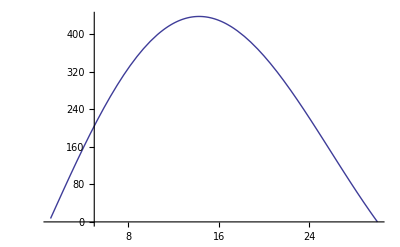

```mathematica
Plot[{2.01*Abs[Rs[r]/.sol]},{r,rp,r1}]
```

```mathematica
(*Now, do the previous procedure for several values of r1, the position of the mirror:
I approach the value from right and left because dont know the rate of change in the function,    in some cases is very high and then fails from one step to other.*)
```

```mathematica
winit=(0.25+0.000005*I);
ie=0;While[ie<201,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=rp+10^(-8);r1=30+ie/5; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);

sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
radit[ie]=r1;
winit=wres-0.001;
ie=ie+1
]
t1r=Table[{N[radit[n],10],Re[witer[n]]},{n,0,200}];
t2r=Table[{N[radit[n],10],Im[witer[n]]},{n,0,200}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

{{30.,1.96319×10^-9},{30.2,1.99606×10^-9},{30.4,2.02315×10^-9},{30.6,2.04499×10^-9},{30.8,2.06243×10^-9},{31.,2.0751×10^-9},{31.2,2.08414×10^-9},{31.4,2.08897×10^-9},{31.6,2.07625×10^-9},{31.8,2.0901×10^-9},{32.,2.08626×10^-9},{32.2,2.07991×10^-9},{32.4,2.0713×10^-9},{32.6,2.06055×10^-9},{32.8,2.04813×10^-9},{33.,2.05024×10^-9},{33.2,2.01864×10^-9},{33.4,2.00198×10^-9},{33.6,1.98595×10^-9},{33.8,1.96485×10^-9},{34.,1.94494×10^-9},{34.2,1.92405×10^-9},{34.4,1.90254×10^-9},{34.6,1.8804×10^-9},{34.8,1.85775×10^-9},{35.,1.83464×10^-9},{35.2,1.81121×10^-9},{35.4,1.78739×10^-9},{35.6,1.75636×10^-9},{35.8,1.73906×10^-9},{36.,1.71466×10^-9},{36.2,1.69004×10^-9},{36.4,1.66565×10^-9},{36.6,1.64102×10^-9},{36.8,1.6165×10^-9},{37.,1.59194×10^-9},{37.2,1.5676×10^-9},{37.4,1.54324×10^-9},{37.6,1.51896×10^-9},{37.8,1.49497×10^-9},{38.,1.47102×10^-9},{38.2,1.44735×10^-9},{38.4,1.42381×10^-9},{38.6,1.39935×10^-9},{38.8,1.37749×10^-9},{39.,1.35466×10^-9},{39.2,1.33497×10^-9},{39.4,1.30979×10^-9},{39.6,1.28771×10^-9},{39.8,1.26593×10^-9},{40.,1.24448×10^-9},{40.2,1.22321×10^-9},{40.4,1.20229×10^-9},{40.6,1.1817×10^-9},{40.8,1.16113×10^-9},{41.,1.14124×10^-9},{41.2,1.12148×10^-9},{41.4,1.10204×10^-9},{41.6,1.08286×10^-9},{41.8,1.06403×10^-9},{42.,1.04541×10^-9},{42.2,1.02709×10^-9},{42.4,1.00912×10^-9},{42.6,9.91442×10^-10},{42.8,9.73503×10^-10},{43.,9.56912×10^-10},{43.2,9.40088×10^-10},{43.4,9.23535×10^-10},{43.6,9.07261×10^-10},{43.8,8.91256×10^-10},{44.,8.75515×10^-10},{44.2,8.60561×10^-10},{44.4,8.44973×10^-10},{44.6,8.27851×10^-10},{44.8,8.15405×10^-10},{45.,8.00984×10^-10},{45.2,7.86774×10^-10},{45.4,7.74137×10^-10},{45.6,7.59362×10^-10},{45.8,7.45985×10^-10},{46.,7.29166×10^-10},{46.2,7.19919×10^-10},{46.4,7.07209×10^-10},{46.6,7.00413×10^-10},{46.8,6.82608×10^-10},{47.,6.70607×10^-10},{47.2,6.58717×10^-10},{47.4,6.47297×10^-10},{47.6,6.3601×10^-10},{47.8,6.2483×10^-10},{48.,6.13907×10^-10},{48.2,6.03183×10^-10},{48.4,5.92653×10^-10},{48.6,5.82324×10^-10},{48.8,5.72188×10^-10},{49.,5.62244×10^-10},{49.2,5.5247×10^-10},{49.4,5.42885×10^-10},{49.6,5.33471×10^-10},{49.8,5.24249×10^-10},{50.,5.15189×10^-10},{50.2,5.06299×10^-10},{50.4,4.97678×10^-10},{50.6,4.89067×10^-10},{50.8,4.80612×10^-10},{51.,4.72514×10^-10},{51.2,4.64267×10^-10},{51.4,4.56326×10^-10},{51.6,4.48532×10^-10},{51.8,4.4098×10^-10},{52.,4.33377×10^-10},{52.2,4.26009×10^-10},{52.4,4.18777×10^-10},{52.6,4.11658×10^-10},{52.8,4.04714×10^-10},{53.,3.97879×10^-10},{53.2,3.91191×10^-10},{53.4,3.84586×10^-10},{53.6,3.78×10^-10},{53.8,3.71683×10^-10},{54.,3.65555×10^-10},{54.2,3.59475×10^-10},{54.4,3.53445×10^-10},{54.6,3.47558×10^-10},{54.8,3.42274×10^-10},{55.,3.36104×10^-10},{55.2,3.30536×10^-10},{55.4,3.25069×10^-10},{55.6,3.19702×10^-10},{55.8,3.14434×10^-10},{56.,3.09262×10^-10},{56.2,3.04184×10^-10},{56.4,2.99197×10^-10},{56.6,2.94306×10^-10},{56.8,2.89364×10^-10},{57.,2.84791×10^-10},{57.2,2.80129×10^-10},{57.4,2.75601×10^-10},{57.6,2.71155×10^-10},{57.8,2.6675×10^-10},{58.,2.62444×10^-10},{58.2,2.58216×10^-10},{58.4,2.54068×10^-10},{58.6,2.49985×10^-10},{58.8,2.4598×10^-10},{59.,2.42062×10^-10},{59.2,2.38187×10^-10},{59.4,2.34726×10^-10},{59.6,2.30622×10^-10},{59.8,2.27008×10^-10},{60.,2.23607×10^-10},{60.2,2.19881×10^-10},{60.4,2.1642×10^-10},{60.6,2.13007×10^-10},{60.8,2.09665×10^-10},{61.,2.06975×10^-10},{61.2,2.0306×10^-10},{61.4,1.99982×10^-10},{61.6,1.96854×10^-10},{61.8,1.93792×10^-10},{62.,1.90784×10^-10},{62.2,1.87865×10^-10},{62.4,1.84927×10^-10},{62.6,1.82068×10^-10},{62.8,1.79283×10^-10},{63.,1.76508×10^-10},{63.2,1.73801×10^-10},{63.4,1.71218×10^-10},{63.6,1.68524×10^-10},{63.8,1.65955×10^-10},{64.,1.63173×10^-10},{64.2,1.6093×10^-10},{64.4,1.58506×10^-10},{64.6,1.56108×10^-10},{64.8,1.53751×10^-10},{65.,1.51435×10^-10},{65.2,1.49158×10^-10},{65.4,1.46918×10^-10},{65.6,1.44764×10^-10},{65.8,1.42554×10^-10},{66.,1.40425×10^-10},{66.2,1.38334×10^-10},{66.4,1.36228×10^-10},{66.6,1.34258×10^-10},{66.8,1.32253×10^-10},{67.,1.30313×10^-10},{67.2,1.28453×10^-10},{67.4,1.26505×10^-10},{67.6,1.24647×10^-10},{67.8,1.2282×10^-10},{68.,1.21018×10^-10},{68.2,1.19364×10^-10},{68.4,1.17517×10^-10},{68.6,1.15805×10^-10},{68.8,1.14131×10^-10},{69.,1.12473×10^-10},{69.2,1.10835×10^-10},{69.4,1.09251×10^-10},{69.6,1.07676×10^-10},{69.8,1.06128×10^-10},{70.,1.04607×10^-10}}

```mathematica
(*Calculate the values leftward*)
```

```mathematica
winit=(0.25+0.000005*I);
ie=0;While[ie<51,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=rp+10^(-8);r1=30-ie/5; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);
(*potsol= 1/f*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2;*)
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
radit[ie]=r1;
winit=wres+0.001;
ie=ie+1

]
t1l=Table[{N[radit[n],10],Re[witer[n]]},{n,0,50}];
t2l=Table[{N[radit[n],10],Im[witer[n]]},{n,0,50}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

```mathematica
(*The imaginary part vs the radius*)
```

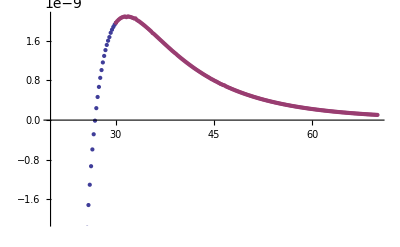

```mathematica
ListPlot[{t2l,t2r},Axes->True]
```

```mathematica
(*Real vs Radius*)
```

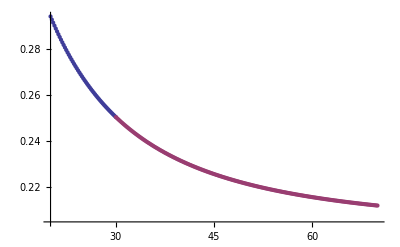

```mathematica
ListPlot[{t1l,t1r}]
```

```mathematica
Export["/home/h/skoli/pt/rnef/mathematica/mirror-radius/mu0.2/Q=0.990/q=0.3/R.dat",Join[t1l,t1r]]
Export["/home/h/skoli/pt/rnef/mathematica/mirror-radius/mu0.2/Q=0.990/q=0.3/I.dat",Join[t2l,t2r]]
```

/home/h/skoli/pt/rnef/mathematica/mirror-radius/mu0.2/Q=0.990/q=0.3/R.dat

/home/h/skoli/pt/rnef/mathematica/mirror-radius/mu0.2/Q=0.990/q=0.3/I.dat

```mathematica
(*This is for estimate the "Analytical" value using Cardoso's bomb *)
```

```mathematica
(*Radius*)
```

```mathematica
rp=M+Sqrt[M^2-Q^2]
rm=M-Sqrt[M^2-Q^2]
rmirror=40
```

1.6

0.4

40

```mathematica
(*Frequencies*)
```

```mathematica
wc=qscal*Q/rp
wtilde=(wa-wc)*(rp^2/(rp-rm))
```

0.45

2.13333 (-0.45+wa)

```mathematica
(*Nodes*)
```

```mathematica
n=0
```

0

```mathematica
(*First aproximation, the root of the Bessel function (has to be the n+1 root, otherwise the 1st is zero!)*)
```

```mathematica
jl12n=N[BesselJZero[l+1/2,n+1],10]
```

4.493409459

```mathematica
wfa=jl12n/rmirror
```

0.1123352365

```mathematica
(*Let's calculate the imaginary part, delta, we need some definitions in advance*)
```

```mathematica
Product[i^2+4*wtilde^2,{i,1,l}]
```

1+18.2044 (-0.45+wa)^2

```mathematica
gamm=(Factorial[l]/Factorial2[(2*l-1)])^2*rp^2*(rp-rm)^(2*l)/Factorial[2*l]/Factorial[2*l+1]*2/(2*l+1)*Product[i^2+4*wtilde^2,{i,1,l}]*jl12n^(2*l+1)
```

18.5805 (1+18.2044 (-0.45+wa)^2)

```mathematica
Dbess=D[BesselJ[l+1/2,x],x]/.x->jl12n
```

-0.367413504

```mathematica
f1=(-1)^(l)*BesselJ[-l-1/2,jl12n]/Dbess
```

1.049528

```mathematica
f2=(wfa-wc)/rmirror^(2*l+2)
```

-1.319×10^-7

```mathematica
(*Imaginary part delta*)
```

```mathematica
deltat=-gamm*f1*f2/.wa->wfa
```

7.91099×10^-6

```mathematica
(*make a list of the 1/r decay*)
```

```mathematica
tan=Table[jl12n/i,{i,50}];
```

```mathematica
(*Compare the behaviour of Re[w] in a plot*)
```



```mathematica
ListPlot[{t1l,t1r,tan}]
```